#### HW(do this for 5 extra pts on the Midterm exam) Calculate,plot and explain the meaning of the hedge for digital put (1 for S<k,and 0 for S>k)if r=3%,𝔻=0,t=2013,T=2014,k=100,S=100,and volatility is time periodic σ(t)=.2+.05Cos[2 π t]. Hint: use this to calculate the constant-coefficient digital put ;and then use: {r→1/(T-t)Integrate[r[τ],{τ,t,T}],𝔻→1/(T-t)Integrate[𝔻[τ],{τ,t,T}],σ^2→1/(T-t)Integrate[σ[τ]^2,{τ,t,T}]}

```mathematica
Subscript[𝕧, ϕ_,r_,𝔻_,σ_][τ_,x_]:=1/(2 √(π τ)) ⅇ^(x (1/2-(r-𝔻)/σ^2)-((4 r^2+4 r (σ^2-2 𝔻)+(σ^2+2 𝔻)^2) τ)/(4 σ^4)) Integrate[ⅇ^(-ξ (1/2-(r-𝔻)/σ^2)-(ξ-x)^2/(4 τ)) ϕ[ⅇ^ξ],{ξ,-∞,∞},Assumptions->τ>0]
```

```mathematica
ContractPayoff[S_]:=Piecewise[{{1,S<k},{0,S>k}}]
```

```mathematica
Subscript[𝕧, ContractPayoff,r,𝔻,σ][τ,x]/.{τ->1/2 (T-t) σ^2,x->Log[S]}//Simplify
```

Piecewise[{{(ⅇ^(r (t-T)) (Erf[(√(((t-T) (2 r-2 𝔻-σ^2)+2 Log[k]-2 Log[S])^2))/(2 √2 √(-(t-T) σ^2))] ((t-T) (2 r-2 𝔻-σ^2)+2 Log[k]-2 Log[S])+√(((t-T) (2 r-2 𝔻-σ^2)+2 Log[k]-2 Log[S])^2)))/(2 √(((t-T) (2 r-2 𝔻-σ^2)+2 Log[k]-2 Log[S])^2)), k>0}, {0, True}}]

```mathematica
Subscript[V, r_,T_,𝔻_,σ_,k_][t_,S_]=(Subscript[𝕧, ContractPayoff,r,𝔻,σ][τ,x]/.{τ->1/2 (T-t) σ^2,x->Log[S]}//Simplify)[[1,1,1]]
```

(ⅇ^(r (t-T)) (Erf[(√(((t-T) (2 r-2 𝔻-σ^2)+2 Log[k]-2 Log[S])^2))/(2 √2 √(-(t-T) σ^2))] ((t-T) (2 r-2 𝔻-σ^2)+2 Log[k]-2 Log[S])+√(((t-T) (2 r-2 𝔻-σ^2)+2 Log[k]-2 Log[S])^2)))/(2 √(((t-T) (2 r-2 𝔻-σ^2)+2 Log[k]-2 Log[S])^2))

```mathematica
Subscript[w, r_,T_,𝔻_,σ_,k_][t_,S_]=Subscript[V, r,T,𝔻,σ,k][t,S]/.{r->1/(T-t)Integrate[r[τ],{τ,t,T}],𝔻->1/(T-t)Integrate[𝔻[τ],{τ,t,T}],σ^2->1/(T-t)Integrate[σ[τ]^2,{τ,t,T}]}
```

(ⅇ^(((t-T) ∫_t^T r[τ]ⅆτ)/(-t+T)) (Erf[(√(((t-T) ((2 ∫_t^T r[τ]ⅆτ)/(-t+T)-(2 ∫_t^T 𝔻[τ]ⅆτ)/(-t+T)-(∫_t^T σ[τ]^2 ⅆτ)/(-t+T))+2 Log[k]-2 Log[S])^2))/(2 √2 √(-((t-T) ∫_t^T σ[τ]^2 ⅆτ)/(-t+T)))] ((t-T) ((2 ∫_t^T r[τ]ⅆτ)/(-t+T)-(2 ∫_t^T 𝔻[τ]ⅆτ)/(-t+T)-(∫_t^T σ[τ]^2 ⅆτ)/(-t+T))+2 Log[k]-2 Log[S])+√(((t-T) ((2 ∫_t^T r[τ]ⅆτ)/(-t+T)-(2 ∫_t^T 𝔻[τ]ⅆτ)/(-t+T)-(∫_t^T σ[τ]^2 ⅆτ)/(-t+T))+2 Log[k]-2 Log[S])^2)))/(2 √(((t-T) ((2 ∫_t^T r[τ]ⅆτ)/(-t+T)-(2 ∫_t^T 𝔻[τ]ⅆτ)/(-t+T)-(∫_t^T σ[τ]^2 ⅆτ)/(-t+T))+2 Log[k]-2 Log[S])^2))

```mathematica
g[S_]=w_(.03&,1,.02&,.3+.04Cos[4*2 π #]&,100)[0,S]
```

(0.485223 (Erf[1.17331 √((9.28114-2 Log[S])^2)] (9.28114-2 Log[S])+√((9.28114-2 Log[S])^2)))/(√((9.28114-2 Log[S])^2))

```mathematica
h[S_]=V_(.03,1,.02,.3+.04Cos[4*2 π 0],100)[0,S]
```

(0.485223 (Erf[1.03986 √((9.30594-2 Log[S])^2)] (9.30594-2 Log[S])+√((9.30594-2 Log[S])^2)))/(√((9.30594-2 Log[S])^2))

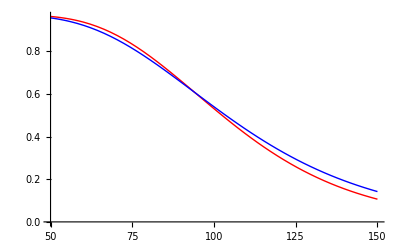

```mathematica
Plot[{g[S],h[S]},{S,50,150},PlotStyle->{Red,Blue}]
```

## Experiment with hedging

```mathematica
With[{T=2014,r=.03,𝔻=0,k=100},Subscript[V, r,T,𝔻,.3+.04Cos[4*2 π 2013],k][2013,100]]
```

0.516843

To see hedging in action, we shall simulate the stock(i.e., the underlying)dynamics

```mathematica
T=2014;r=.03;𝔻=0;k=100;t0=2013;S0=100;K=1000;
```

```mathematica
?#
```

# represents the first argument supplied to a pure function. 
#n represents the n^th argument.

```mathematica
Subscript[V, r,T,𝔻,.3+.04Cos[4*2 π #]&,k][t0,S0]
```

(0.485223 (Erf[(√((-0.06+(0.3+0.04 Cos[4 2 π #1]&)^2)^2))/(2 √2 √((0.3+0.04 Cos[4 2 π #1]&)^2))] (-0.06+(0.3+0.04 Cos[4 2 π #1]&)^2)+√((-0.06+(0.3+0.04 Cos[4 2 π #1]&)^2)^2)))/(√((-0.06+(0.3+0.04 Cos[4 2 π #1]&)^2)^2))

```mathematica
dt=(T-t0)/K//N
```

0.001

```mathematica
dB=Table[Sqrt[dt]Random[NormalDistribution[]],{K}];
```

```mathematica
FF[{t_,S_},db_]:={t+dt,S+S (.3+.04Cos[4*2 π (t+dt)] )db}
```

```mathematica
SList=FoldList[FF,{t0,S0},dB];
```

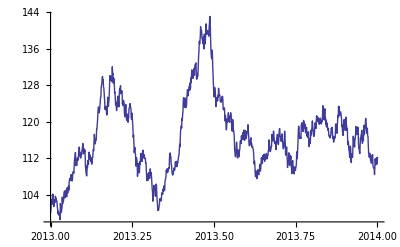

```mathematica
ListPlot[SList,Joined-> True]
```

```mathematica
Subscript[v, r_,T_,𝔻_,σ_,k_][{t_,S_}]:=Subscript[V, r,T,𝔻,σ,k][t,S]
```

```mathematica
Subscript[v, r,T,𝔻,.3+.04Cos[4*2 π t0],k][t0,S0]
```

v_(0.03,2014,0,0.34,100)[2013,100]

```mathematica
Subscript[v, r,T,𝔻,#&,k][SList[[1]]]
```

(0.485223 (Erf[(√((-0.06+(#1&)^2)^2))/(2 √2 √((#1&)^2))] (-0.06+(#1&)^2)+√((-0.06+(#1&)^2)^2)))/(√((-0.06+(#1&)^2)^2))

We have a portifolio consisting of:
one contract
?number of underlying stocks(given by BS hedging formula)
?amount of money in cash account(this is determined by selling and buying stocks in order to maintain the BS hedging)
Furthermore, if the hedging is perfect then this portifolio should evolve as money in the bank

```mathematica
Off[General::unfl]
```

```mathematica
vList=Subscript[v, r,T,𝔻,#&,k]/@SList;
timeList =Transpose[SList][[1]];
```

```mathematica
ListPlot[Transpose[{timeList,vList}],Joined-> True]
```

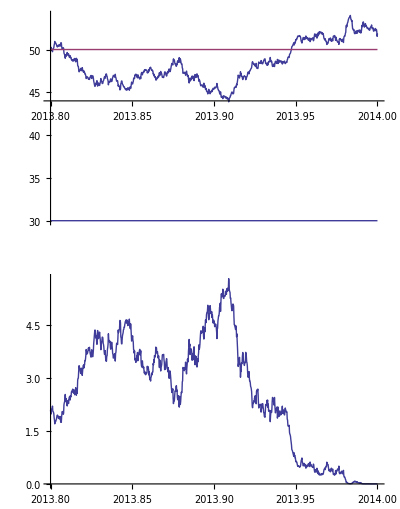

```mathematica
GraphicsGrid[{{Show[ListPlot[SList,Joined-> True],Plot[{k},{t,t0,T}],PlotRange->{0, All}]},{ListPlot[Transpose[{timeList,vList}],Joined-> True]}}]
```

```mathematica
Off[General::unfl]
```

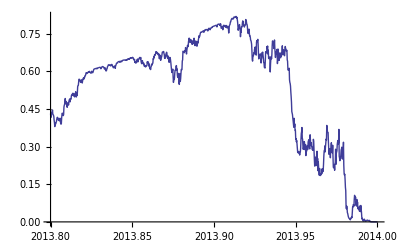

```mathematica
ListPlot[Transpose[{timeList,HedgeList=-Derivative[{0,1}][Subscript[v, r,T,𝔻,#&,k]]/@SList}],Joined-> True]
```

```mathematica
Take[HedgeList,2]
```

{0.431242,0.415849}

```mathematica
Take[-Differences[HedgeList]Drop[Transpose[SList][[2]],1],2]
```

{0.77398,-0.826793}

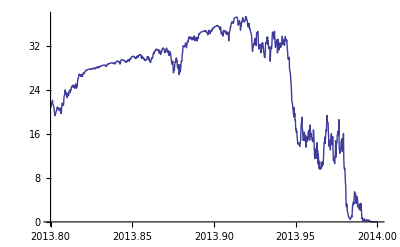

```mathematica
ListPlot[Transpose[
{timeList,HedgeValueList=-Derivative[{0,1}][Subscript[v, r,T,𝔻,σ,k1,k3]][#]#[[2]]&/@SList}],Joined-> True]
```

```mathematica
HedgingCashInflux=-Differences[HedgeList]Drop[Transpose[SList][[2]],1];
```

```mathematica
DividendCashInflux=𝔻 Drop[HedgeList,1]Drop[Transpose[SList][[2]],1]dt;
```

```mathematica
CashFunction[PrevCash_,CashInflux_]:=PrevCash+r PrevCash dt+CashInflux
```

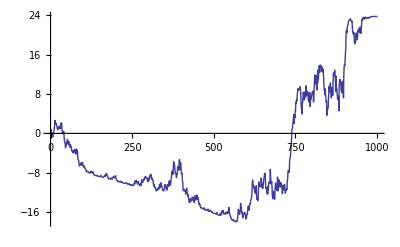

```mathematica
ListPlot[cashEvolustion=FoldList[CashFunction,0,HedgingCashInflux+DividendCashInflux],Joined-> True]
```

```mathematica
ListPlot[Transpose[{timeList,HedgeValueList=-Derivative[{0,1}][Subscript[v, r,T,𝔻,σ,k1,k3]][#]#[[2]]&/@SList}],Joined-> True]
```

-Graphics-

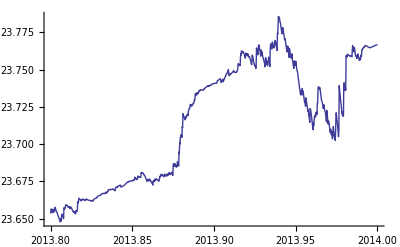

```mathematica
ListPlot[Transpose[{timeList,bsList+HedgeValueList+cashEvolustion}],Joined-> True,PlotRange->{0,All}]
```